### Definitions

```mathematica
Np =3;
d = 1;
lm = 1;
lp[k_]:=((k+1)^(1/4))/lm;
$Assumptions = -1<k && Im[k]==0
xcoord={x1,x2,x3}
xpcoord = {x1p,x2p,x3p}
A[lp_]:=1/(2 lp^2);
B[lm_,lp_, Np_]:=-1/(2Np) (1/lm^2-1/lp^2);
```

-1<k&&Im[k]==0

{x1,x2,x3}

{x1p,x2p,x3p}

### Coefficients from Analytical Calculation

```mathematica
p000int[a_, b_] := (2 √(a^2 (a-3 b)))/(√a (2 a-3 b))
p111int[a_,b_]:= 0


p222int[a_,b_]:=(225 √(a^2 (a-3 b)) b^6)/(4 √a (2 a-3 b)^7)
p333int[a_,b_]:=0
p444int[a_,b_]:=(4002075 √(a^2 (a-3 b)) b^12)/(256 √a (2 a-3 b)^13)

p555int[a_,b_]:=0
p666int[a_,b_]:=(13031023005 √(a^2 (a-3 b)) b^18)/(2048 √a (2 a-3 b)^19)
p777int[a_,b_]:=0
p888int[a_,b_]:=(3199527555739515 √(a^2 (a-3 b)) b^24)/(1048576 √a (2 a-3 b)^25)
```

```mathematica
p00i[a_,b_]:=-(2 √(a^2 (a-3 b)))/(√a (2 a-3 b))+(a √((a (a-3 b))/(a-2 b)) √((a (a-2 b))/(a-b)))/(√((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))
p11i[a_,b_]:=(a √((a (a-3 b))/(a-2 b)) √((a (a-2 b))/(a-b)) b^2 (4 a^2-12 a b+11 b^2))/(16 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))
p22i[a_,b_]:=-(225 √(a^2 (a-3 b)) b^6)/(4 √a (2 a-3 b)^7)+(3 a √((a (a-3 b))/(a-2 b)) √((a (a-2 b))/(a-b)) b^4 (48 a^4-288 a^3 b+744 a^2 b^2-936 a b^3+467 b^4))/(1024 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^4 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))
p33i[a_,b_]:=1/(16384 a^2 (a-2 b)^7 (a-b)^6)5 √((a (a-3 b))/(a-2 b)) √((a (a-2 b))/(a-b)) b^6 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (320 a^6-2880 a^5 b+12240 a^4 b^2-30240 a^3 b^3+44220 a^2 b^4-35460 a b^5+12031 b^6)
p44i[a_,b_]:=-(4002075 √(a^2 (a-3 b)) b^12)/(256 √a (2 a-3 b)^13)+1/(4194304 a^2 (a-2 b)^9 (a-b)^8)35 √((a (a-3 b))/(a-2 b)) √((a (a-2 b))/(a-b)) b^8 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (8960 a^8-107520 a^7 b+636160 a^6 b^2-2338560 a^5 b^3+5648160 a^4 b^4-8971200 a^3 b^5+9033808 a^2 b^6-5237904 a b^7+1334531 b^8)
p55i[a_,b_]:=1/(67108864 a^3 (a-2 b)^12 (a-b)^9)63 √((a (a-3 b))/(a-2 b)) ((a (a-2 b))/(a-b))^(3/2) b^10 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (64512 a^10-967680 a^9 b+7338240 a^8 b^2-35804160 a^7 b^3+120462720 a^6 b^4-285538176 a^5 b^5+476693280 a^4 b^6-549702720 a^3 b^7+417618540 a^2 b^8-188437860 a b^9+38319493 b^10)
p66i[a_,b_]:=1/(4294967296 a^2)231 b^12 (-(118303185960960 a^(3/2) √(a^2 (a-3 b)) b^6)/(2 a-3 b)^19+1/((a-2 b)^13 (a-b)^12)√((a (a-3 b))/(a-2 b)) √((a (a-2 b))/(a-b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (946176 a^12-17031168 a^11 b+157538304 a^10 b^2-958003200 a^9 b^3+4130945280 a^8 b^4-13013941248 a^7 b^5+30318968064 a^6 b^6-52271315712 a^5 b^7+65958068880 a^4 b^8-59305672800 a^3 b^9+36037713624 a^2 b^10-13283012952 a b^11+2245472791 b^12))
p77i[a_,b_]:=(429 √((a (a-3 b))/(a-2 b)) √((a (a-2 b))/(a-b)) b^14 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (7028736 a^14-147603456 a^13 b+1611337728 a^12 b^2-11734474752 a^11 b^3+61707469824 a^10 b^4-242466352128 a^9 b^5+724695299328 a^8 b^6-1662229730304 a^7 b^7+2929861910976 a^6 b^8-3942307841472 a^5 b^9+3982829074224 a^4 b^10-2928390008544 a^3 b^11+1480999648492 a^2 b^12-461113630068 a b^13+66682885991 b^14))/(68719476736 a^2 (a-2 b)^15 (a-b)^14)
p88i[a_,b_]:=1/(70368744177664 a^2)6435 b^16 (-(33367002269211426816 a^(3/2) √(a^2 (a-3 b)) b^8)/(2 a-3 b)^25+1/((a-2 b)^17 (a-b)^16)√((a (a-3 b))/(a-2 b)) √((a (a-2 b))/(a-b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (421724160 a^16-10121379840 a^15 b+127360696320 a^14 b^2-1080457297920 a^13 b^3+6703902965760 a^12 b^4-31559094927360 a^11 b^5+115104938876928 a^10 b^6-329501995130880 a^9 b^7+745534944760320 a^8 b^8-1335365949265920 a^7 b^9+1885527012328960 a^6 b^10-2075829473862144 a^5 b^11+1746461011364160 a^4 b^12-1085404339393920 a^3 b^13+469917027760800 a^2 b^14-126622609950240 a b^15+15997721271011 b^16))
```

```mathematica
p0i[a_,b_]:=-(a √((a (a-3 b))/(a-2 b)) √((a (a-2 b))/(a-b)))/(√((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(√a √(2 π))/(√((2 a^2-5 a b+b^2)/(a-2 b)) √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b)))
p1i[a_,b_]:=-((a √((a (a-3 b))/(a-2 b)) √((a (a-2 b))/(a-b)) b^2 (4 a^2-12 a b+11 b^2))/(16 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))))+(a^(3/2) b^2)/((a-2 b) ((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2))^(3/2) π ((2 a^2-5 a b+b^2)/(2 a π-4 b π))^(3/2) √((a π-2 b π)/(2 a^2-6 a b)))
p2i[a_,b_]:=-((3 a √((a (a-3 b))/(a-2 b)) √((a (a-2 b))/(a-b)) b^4 (48 a^4-288 a^3 b+744 a^2 b^2-936 a b^3+467 b^4))/(1024 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^4 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))))+(√a b^2 (4 a^2-12 a b+17 b^2) √(π/2))/(√((2 a^2-5 a b+b^2)/(a-2 b)) (4 a^2-12 a b+5 b^2)^2 √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b)))
p3i[a_,b_]:=-1/(16384 a^2 (a-2 b)^7 (a-b)^6)5 √((a (a-3 b))/(a-2 b)) √((a (a-2 b))/(a-b)) b^6 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (320 a^6-2880 a^5 b+12240 a^4 b^2-30240 a^3 b^3+44220 a^2 b^4-35460 a b^5+12031 b^6)+(√a b^4 (12 a^2-36 a b+35 b^2) √(2 π))/(√((2 a^2-5 a b+b^2)/(a-2 b)) (4 a^2-12 a b+5 b^2)^3 √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b)))
p4i[a_,b_]:=-1/(4194304 a^2 (a-2 b)^9 (a-b)^8)35 √((a (a-3 b))/(a-2 b)) √((a (a-2 b))/(a-b)) b^8 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (8960 a^8-107520 a^7 b+636160 a^6 b^2-2338560 a^5 b^3+5648160 a^4 b^4-8971200 a^3 b^5+9033808 a^2 b^6-5237904 a b^7+1334531 b^8)+(√a b^4 (48 a^4-288 a^3 b+1032 a^2 b^2-1800 a b^3+1235 b^4) √(π/2))/(4 √((2 a^2-5 a b+b^2)/(a-2 b)) (4 a^2-12 a b+5 b^2)^4 √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b)))
p5i[a_,b_]:=(√a b^6 (240 a^4-1440 a^3 b+3880 a^2 b^2-5160 a b^3+2783 b^4))/(2 √((a-2 b)/(a^2-3 a b)) √((2 a^2-5 a b+b^2)/(a-2 b)) (4 a^2-12 a b+5 b^2)^5 √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)))-1/(67108864 a^3 (a-2 b)^12 (a-b)^9)63 √((a (a-3 b))/(a-2 b)) ((a (a-2 b))/(a-b))^(3/2) b^10 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (64512 a^10-967680 a^9 b+7338240 a^8 b^2-35804160 a^7 b^3+120462720 a^6 b^4-285538176 a^5 b^5+476693280 a^4 b^6-549702720 a^3 b^7+417618540 a^2 b^8-188437860 a b^9+38319493 b^10)
p6i[a_,b_]:=(√a b^6 (320 a^6-2880 a^5 b+16560 a^4 b^2-56160 a^3 b^3+109740 a^2 b^4-115380 a b^5+51109 b^6))/(8 √((a-2 b)/(a^2-3 a b)) √((2 a^2-5 a b+b^2)/(a-2 b)) (4 a^2-12 a b+5 b^2)^6 √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)))-(231 √((a (a-3 b))/(a-2 b)) √((a (a-2 b))/(a-b)) b^12 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (946176 a^12-17031168 a^11 b+157538304 a^10 b^2-958003200 a^9 b^3+4130945280 a^8 b^4-13013941248 a^7 b^5+30318968064 a^6 b^6-52271315712 a^5 b^7+65958068880 a^4 b^8-59305672800 a^3 b^9+36037713624 a^2 b^10-13283012952 a b^11+2245472791 b^12))/(4294967296 a^2 (a-2 b)^13 (a-b)^12)
p7i[a_,b_]:=(√a b^8 (2240 a^6-20160 a^5 b+89040 a^4 b^2-231840 a^3 b^3+362292 a^2 b^4-315756 a b^5+118771 b^6))/(4 √((a-2 b)/(a^2-3 a b)) √((2 a^2-5 a b+b^2)/(a-2 b)) (4 a^2-12 a b+5 b^2)^7 √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)))-(429 √((a (a-3 b))/(a-2 b)) √((a (a-2 b))/(a-b)) b^14 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (7028736 a^14-147603456 a^13 b+1611337728 a^12 b^2-11734474752 a^11 b^3+61707469824 a^10 b^4-242466352128 a^9 b^5+724695299328 a^8 b^6-1662229730304 a^7 b^7+2929861910976 a^6 b^8-3942307841472 a^5 b^9+3982829074224 a^4 b^10-2928390008544 a^3 b^11+1480999648492 a^2 b^12-461113630068 a b^13+66682885991 b^14))/(68719476736 a^2 (a-2 b)^15 (a-b)^14)
p8i[a_,b_]:=(√a b^8 (8960 a^8-107520 a^7 b+851200 a^6 b^2-4273920 a^5 b^3+13712160 a^4 b^4-28324800 a^3 b^5+36701392 a^2 b^6-27276816 a b^7+8915075 b^8))/(64 √((a-2 b)/(a^2-3 a b)) √((2 a^2-5 a b+b^2)/(a-2 b)) (4 a^2-12 a b+5 b^2)^8 √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)))-(6435 √((a (a-3 b))/(a-2 b)) √((a (a-2 b))/(a-b)) b^16 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (421724160 a^16-10121379840 a^15 b+127360696320 a^14 b^2-1080457297920 a^13 b^3+6703902965760 a^12 b^4-31559094927360 a^11 b^5+115104938876928 a^10 b^6-329501995130880 a^9 b^7+745534944760320 a^8 b^8-1335365949265920 a^7 b^9+1885527012328960 a^6 b^10-2075829473862144 a^5 b^11+1746461011364160 a^4 b^12-1085404339393920 a^3 b^13+469917027760800 a^2 b^14-126622609950240 a b^15+15997721271011 b^16))/(70368744177664 a^2 (a-2 b)^17 (a-b)^16)
```

```mathematica
p0vac[a_,b_]:= 1-p0i[a,b]-p00i[a,b]-p000int[a,b]
p1vac[a_,b_]:= 1-p1i[a,b]-p11i[a,b]-p111int[a,b]
p2vac[a_,b_]:= 1-p2i[a,b]-p22i[a,b]-p222int[a,b]
p3vac[a_,b_]:= 1-p3i[a,b]-p33i[a,b]-p333int[a,b]
p4vac[a_,b_]:= 1-p4i[a,b]-p44i[a,b]-p444int[a,b]
p5vac[a_,b_]:= 1-p5i[a,b]-p55i[a,b]-p555int[a,b]
p6vac[a_,b_]:= 1-p6i[a,b]-p66i[a,b]-p666int[a,b]
p7vac[a_,b_]:= 1-p7i[a,b]-p77i[a,b]-p777int[a,b]
p8vac[a_,b_]:= 1-p8i[a,b]-p88i[a,b]-p888int[a,b]
```

## Determining Entanglement

```mathematica
acc = 20
```

20

```mathematica
s[i_]:=If[i==0,0,-i*Log[i]]
logc[i_]:=If[i≤10^(-acc),0,Log[i]]
```

```mathematica
q0[k_] := {p0vac[A[lp[k]],B[lm,lp[k], Np]], p1vac[A[lp[k]],B[lm,lp[k], Np]], p2vac[A[lp[k]],B[lm,lp[k], Np]], p3vac[A[lp[k]],B[lm,lp[k], Np]], p4vac[A[lp[k]],B[lm,lp[k], Np]], p5vac[A[lp[k]],B[lm,lp[k], Np]], p6vac[A[lp[k]],B[lm,lp[k], Np]], p7vac[A[lp[k]],B[lm,lp[k], Np]],p8vac[A[lp[k]],B[lm,lp[k], Np]]}
q1[k_] :={p0i[A[lp[k]],B[lm,lp[k], Np]], p1i[A[lp[k]],B[lm,lp[k], Np]],p2i[A[lp[k]],B[lm,lp[k], Np]], p3i[A[lp[k]],B[lm,lp[k], Np]], p4i[A[lp[k]],B[lm,lp[k], Np]], p5i[A[lp[k]],B[lm,lp[k], Np]], p6i[A[lp[k]],B[lm,lp[k], Np]],p7i[A[lp[k]],B[lm,lp[k], Np]], p8i[A[lp[k]],B[lm,lp[k], Np]]}
q2[k_] :={p00i[A[lp[k]],B[lm,lp[k], Np]],p11i[A[lp[k]],B[lm,lp[k], Np]], p22i[A[lp[k]],B[lm,lp[k], Np]], p33i[A[lp[k]],B[lm,lp[k], Np]], p44i[A[lp[k]],B[lm,lp[k], Np]], p55i[A[lp[k]],B[lm,lp[k], Np]], p66i[A[lp[k]],B[lm,lp[k], Np]],p77i[A[lp[k]],B[lm,lp[k], Np]], p88i[A[lp[k]],B[lm,lp[k], Np]]}
q3[k_] :={p000int[A[lp[k]],B[lm,lp[k], Np]], p111int[A[lp[k]],B[lm,lp[k], Np]],p222int[A[lp[k]],B[lm,lp[k], Np]],p333int[A[lp[k]],B[lm,lp[k], Np]], p444int[A[lp[k]],B[lm,lp[k], Np]], p555int[A[lp[k]],B[lm,lp[k], Np]],p666int[A[lp[k]],B[lm,lp[k], Np]],p777int[A[lp[k]],B[lm,lp[k], Np]], p888int[A[lp[k]],B[lm,lp[k], Np]]}
```

```mathematica
q0[0.9]
```

{0.00713683,0.994352,0.99854,0.999975,0.999997,1.,1.,1.,1.}

```mathematica
(*without SSR, k denotes kappa dimensionless coupling constant and i the mode index*)
e[k_, i_] := s[q0[k][[i+1]]]+s[q1[k][[i+1]]]+s[q2[k][[i+1]]]+s[q3[k][[i+1]]]
i[k_,i_]:= 2*e[k,i]
```

```mathematica
i[0.5,0]
```

0.073747

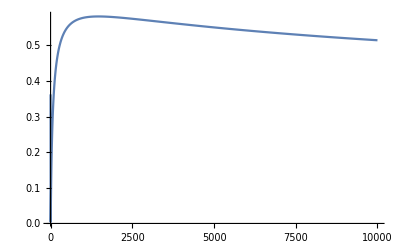

```mathematica
Plot[(i[k,3]), {k,-0.99,10000}, PlotRange->All]
```

```mathematica
kappalogrange[i_]:= If[i≤0, i, 10^(i-1)]
kappalogrange2[i_]:= If[i≤1, i, 10^(i-1)]
export[dataset_,label_]:=Export["/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/data_bosn3d1/"<>ToString[label],dataset, "CSV"]
eexpneg[i_]:=export[Flatten[Table[e[kappalogrange2[k],i], {k,-0.99,1,0.01}]], "emode"<>ToString[i]"neg"]
eexppos[i_]:=export[Flatten[Table[e[kappalogrange2[k],i], {k,1,6,0.01}]], "emode"<>ToString[i]"pos"]

iexpneg[j_]:=export[Flatten[Table[i[kappalogrange2[k],j], {k,-0.99,1,0.01}]], "imode"<>ToString[j]"neg"]

iexppos[j_]:=export[Flatten[Table[i[kappalogrange2[k],j], {k,1,6,0.01}]], "imode"<>ToString[j]"pos"]
```

```mathematica
(*Table[iexpneg[j], {j,0,8}]
Table[iexppos[j], {j,0,8}]*)
```

```mathematica
Table[eexpneg[i], {i,0,2}]
Table[eexppos[i], {i,0,2}]
```

{/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/data_bosn3d1/emode0 neg,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/data_bosn3d1/emode1 neg,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/data_bosn3d1/emode2 neg}

{/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/data_bosn3d1/emode0 pos,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/data_bosn3d1/emode1 pos,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/data_bosn3d1/emode2 pos}